```mathematica
p[z_,1]=1- z^2-4 z^3+4 z^5- z^6+z^8
```

1-z^2-4 z^3+4 z^5-z^6+z^8

```mathematica
p[z_,2]=1-4 z^3- z^4- z^6+4 z^7+z^10
```

1-4 z^3-z^4-z^6+4 z^7+z^10

```mathematica
p[z_,3]=-1+4.4721359549995805 z^3-4.472135954999578 z^9+z^12
```

-1+4.47214 z^3-4.47214 z^9+z^12

```mathematica
p[z_,4]=-1+4.4721359549995805 z^3- z^6+ z^8-4.472135954999577 z^11+z^14
```

-1+4.47214 z^3-z^6+z^8-4.47214 z^11+z^14

```mathematica
p[z_,5]=-1+4.472135954999584 z^3-z^6+ z^10-4.472135954999574 z^13+z^16
```

-1+4.47214 z^3-z^6+z^10-4.47214 z^13+z^16

```mathematica
p[z_,6]=-1+4.472135954999586 z^3- z^6+ z^12-4.472135954999564 z^15+z^18
```

-1.+4.47214 z^3-z^6+z^12-4.47214 z^15+z^18

```mathematica
TableForm[Table[CoefficientList[p[x,i],x],{i,6}]]
```

1 | 0 | -1 | -4 | 0 | 4 | -1 | 0 | 1 |  |  |  |  |  |  |  |  |  | 
1 | 0 | 0 | -4 | -1 | 0 | -1 | 4 | 0 | 0 | 1 |  |  |  |  |  |  |  | 
-1 | 0 | 0 | 4.47214 | 0 | 0 | 0 | 0 | 0 | -4.47214 | 0 | 0 | 1 |  |  |  |  |  | 
-1 | 0 | 0 | 4.47214 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | -4.47214 | 0 | 0 | 1 |  |  |  | 
-1 | 0 | 0 | 4.47214 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | -4.47214 | 0 | 0 | 1 |  | 
-1. | 0 | 0 | 4.47214 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -4.47214 | 0 | 0 | 1

```mathematica
Table[Apply[Plus,Abs[CoefficientList[p[x,i],x]]],{i,6}]
```

{12,12,10.9443,12.9443,12.9443,12.9443}

```mathematica
w=Table[x/.NSolve[p[x,i]==0,x],{i,6}]
```

{{-1.61803,-1.,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.618034,0.809017-1.40126 ⅈ,0.809017+1.40126 ⅈ,1.},{-1.61803,-1.,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.618034,0.809017-1.40126 ⅈ,0.809017+1.40126 ⅈ,1.},{-1.,-0.809017-1.40126 ⅈ,-0.809017+1.40126 ⅈ,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.618034,1.,1.61803},{-1.,-0.809017-1.40126 ⅈ,-0.809017+1.40126 ⅈ,-0.707107-0.707107 ⅈ,-0.707107+0.707107 ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.618034,0.707107-0.707107 ⅈ,0.707107+0.707107 ⅈ,1.,1.61803},{-1.,-0.809017-0.587785 ⅈ,-0.809017+0.587785 ⅈ,-0.809017-1.40126 ⅈ,-0.809017+1.40126 ⅈ,-0.309017-0.951057 ⅈ,-0.309017+0.951057 ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.309017-0.951057 ⅈ,0.309017+0.951057 ⅈ,0.618034,0.809017-0.587785 ⅈ,0.809017+0.587785 ⅈ,1.,1.61803},{-1.,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ,-0.809017-1.40126 ⅈ,-0.809017+1.40126 ⅈ,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.618034,0.866025-0.5 ⅈ,0.866025+0.5 ⅈ,1.,1.61803}}

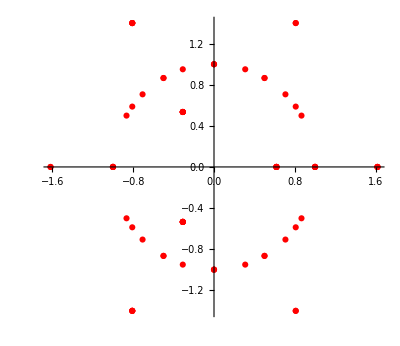

```mathematica
ComplexListPlot[w,PlotStyle->Red,ImageSize->Full]
```